```mathematica
(* Make this notebook standalone *)
(* See: http://stackoverflow.com/questions/4896011/mathematica-separating-notebooks *)
SetOptions[EvaluationNotebook[], CellContext -> Notebook];
```

```mathematica
Force = Subscript[k, b]*T/Subscript[L, p] * (1/(4*(1-l)^2) - 1/4 + l + Sum[Subscript[a, i]*l^(i),{i,2,n}])
```

(T k_b (-1/4+1/(4 (1-l)^2)+l+∑_(i=2)^n l^i a_i))/L_p

```mathematica
ForceNoCoeffs = Force /. Subscript[a, i]-> 0
```

((-1/4+1/(4 (1-l)^2)+l) T k_b)/L_p

```mathematica
(* evidentally, the second solution (of three) converges the best for our regions of interest *)
```

```mathematica
LReal = l /. Solve[ForceNoCoeffs == F,l][[2]];
```

```mathematica
rules = {l -> x/Subscript[L, 0]-F/Subscript[K, 0]}
```

{l→-F/K_0+x/L_0}

```mathematica
ExtensionPerForce = x /. Solve[ (l /. rules) == LReal,x][[1]]
```

L_0 (F/K_0-(-9 T k_b-4 F L_p)/(12 T k_b)+((1+ⅈ √3) (-9 T^2 k_b^2+24 F T k_b L_p-16 F^2 L_p^2))/(24 T k_b (-243 T^3 k_b^3+108 F T^2 k_b^2 L_p-144 F^2 T k_b L_p^2+64 F^3 L_p^3+12 √3 √(135 T^6 k_b^6-108 F T^5 k_b^5 L_p+144 F^2 T^4 k_b^4 L_p^2-64 F^3 T^3 k_b^3 L_p^3))^(1/3))-1/(24 T k_b)(1-ⅈ √3) (-243 T^3 k_b^3+108 F T^2 k_b^2 L_p-144 F^2 T k_b L_p^2+64 F^3 L_p^3+12 √3 √(135 T^6 k_b^6-108 F T^5 k_b^5 L_p+144 F^2 T^4 k_b^4 L_p^2-64 F^3 T^3 k_b^3 L_p^3))^(1/3))

```mathematica
PlotRules = {Subscript[L, p]-> Lp, T-> 1,Subscript[k, b]-> kbT,Subscript[K, 0]-> K0, Subscript[L, 0]-> L0}
```

{L_p→Lp,T→1,k_b→kbT,K_0→K0,L_0→L0}

```mathematica
CForm[ExtensionPerForce /.  PlotRules]
```

L0*(F/K0 - (-9*kbT - 4*F*Lp)/(12.*kbT) + 
     ((1 + Complex(0,1)*Sqrt(3))*(-9*Power(kbT,2) + 24*F*kbT*Lp - 
          16*Power(F,2)*Power(Lp,2)))/
      (24.*kbT*Power(-243*Power(kbT,3) + 108*F*Power(kbT,2)*Lp - 
          144*Power(F,2)*kbT*Power(Lp,2) + 64*Power(F,3)*Power(Lp,3) + 
          12*Sqrt(3)*Sqrt(135*Power(kbT,6) - 108*F*Power(kbT,5)*Lp + 
             144*Power(F,2)*Power(kbT,4)*Power(Lp,2) - 
             64*Power(F,3)*Power(kbT,3)*Power(Lp,3)),0.3333333333333333)) - 
     ((1 - Complex(0,1)*Sqrt(3))*Power(-243*Power(kbT,3) + 108*F*Power(kbT,2)*Lp - 
          144*Power(F,2)*kbT*Power(Lp,2) + 64*Power(F,3)*Power(Lp,3) + 
          12*Sqrt(3)*Sqrt(135*Power(kbT,6) - 108*F*Power(kbT,5)*Lp + 
             144*Power(F,2)*Power(kbT,4)*Power(Lp,2) - 
             64*Power(F,3)*Power(kbT,3)*Power(Lp,3)),0.3333333333333333))/(24.*kbT))

```mathematica
(* make a plot, just to show how this all works for sensibly scaled parameter *)
```

```mathematica
RelativeExtLpIsOne = ExtensionPerForce/Subscript[L, 0]/. { Subscript[L, p]-> 1,Subscript[K, 0]-> 1500,Subscript[k, b]-> 1, T-> 1};
```

```mathematica
RelativeExtLpIsTen = ExtensionPerForce/Subscript[L, 0]/. { Subscript[L, p]-> 10,Subscript[K, 0]-> 1500,Subscript[k, b]-> 1, T-> 1};
```

```mathematica
PlotFunc[x_] := Re[x];
```

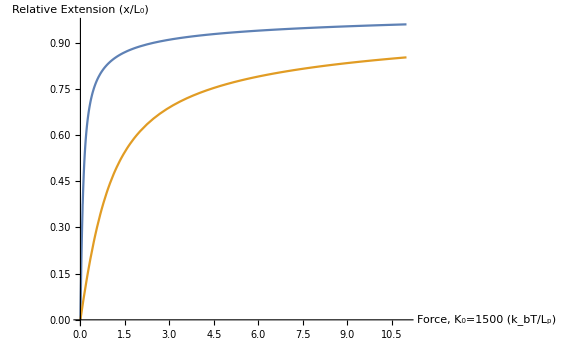

```mathematica
Plot[{PlotFunc[RelativeExtLpIsTen],PlotFunc[RelativeExt]},{F,0,11},PlotRange->All,AxesLabel->{"Force, K_0=1500 (k_bT/L_p)","Relative Extension (x/L_0)"}]
```